```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/phasedata_v2/datav4

```mathematica
chi0=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi0.dat"]],{i,800,870,5}];
chi1=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi1.dat"]],{i,800,870,5}];
chi2=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi2.dat"]],{i,800,870,5}];
chi3=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi3.dat"]],{i,800,870,5}];
chi4=Table[Flatten[Import["./mub"<>ToString[i]<>"/final/buffer/chi4.dat"]],{i,800,870,5}];
r42=chi4/chi2//Quiet;
r21=chi2/chi1//Quiet;
r12=chi1/chi2//Quiet;
r32=chi3/chi2//Quiet;
r31=chi3/chi1//Quiet;
```

```mathematica
r42[[1;;15]][[1;;10]]=1;
```

```mathematica
r42=Import["./output.dat"];
```

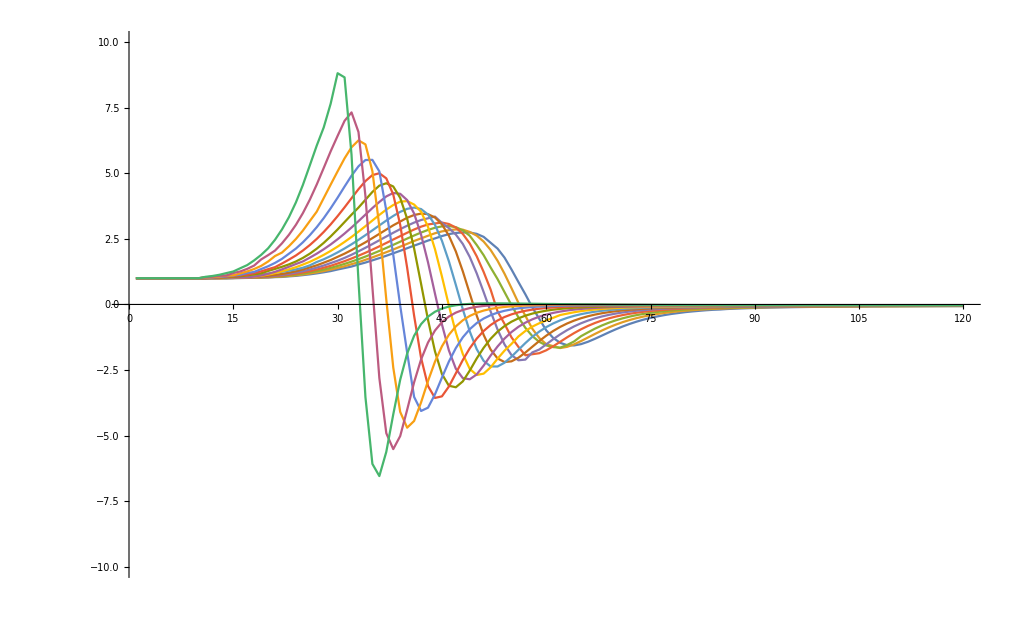

```mathematica
ListLinePlot[Table[r42[[i]],{i,1,15}],PlotRange->{All,{-10,10}}]
```

```mathematica
mub=Table[i,{i,800,870,5}];
T=Table[i,{i,1,120,1}];
```

```mathematica
R42all=Flatten[Table[{x=mub[[j]],y=T[[i]],r42[[j]][[i]]},{i,1,120},{j,1,15}],1];
Export["r42low800to870.dat",R42all]
```

r42low800to870.dat

```mathematica
Dimensions[r42]
```

{15,120}

```mathematica
Export["r42low800to870.dat",r42]
```

r42low800to870.dat